# 15 Stability (cont)

Still looking a bit abstract for a couple of lectures!

## Accuracy/Stability/Backwards Stability

We have an abstract problem f:X→Y with a floating point algorithm f̃:X→Y.

f̃ is accurate if  (|| f̃(x) - f(x) ||)/(||f(x)||)=O(ϵ_mac): 
"Accurate algorithms give nearly the right answer!"

f̃ is stable if  (|| f̃(x) - f(x̃) ||)/(||f(x̃)||)=O(ϵ_machine) for x̃ with (|| x - x̃ ||)/(||x||)=O(ϵ_mac): 
"Stable algorithms give nearly the right answer to nearly the right question!"

f̃ is backwards stable if  f̃(x) = f(x̃) for some x̃ satisfying(|| x - x̃ ||)/(||x||)=O(ϵ_machine) 
“Backwards stable algorithm give the right answer to nearly the right question!”

## Floating Point Ops: +, -, ×, ÷, … are backwards stable

This is going to look a bit “picky”!

Let X=ℝ^2 and write X={x_1,x_2}∈X.  Note, x_1 and x_2 are probably not representable floating point numbers. For instance hey could be π or or e or 1/10.

Approximate by floating point numbers i.e.  (x̃)_1=fl(x_1) and (x̃)_2=fl(x_2).  Remember by our floating point axioms (x̃)_1=x_1(1+ϵ_1) and (x̃)_2=x_2(1+ϵ_2) with both ϵ_1 and ϵ_2 less than ϵ_machine.

### FP Subtraction

FP subtract “⊖” the FP numbers and remember that (x̃)_1⊖(x̃)_2=((x̃)_1-(x̃)_2)(1+ϵ_3)

Combine the bits together  (x̃)_1⊖(x̃)_2=((x̃)_1-(x̃)_2)(1+ϵ_3)=(x_1(1+ϵ_1)-x_2(1+ϵ_2))(1+ϵ_3)

Multiply them all out (x̃)_1⊖(x̃)_2=x_1(1+ϵ_1)(1+ϵ_3)-x_2(1+ϵ_2)(1+ϵ_3)=x_1(1+ϵ_4)-x_2(1+ϵ_5) where ϵ_4=ϵ_1+ϵ_2+ϵ_1 ϵ_2 etc.

Note that |ϵ_4|≤2 ϵ_machine+O(ϵ_machine^2) with the same statement for ϵ_5.

Squint at at this a bit and you see we have all the pieces for backward stability.  We can take C=3.

### Other FP Ops

They all work the same: use the representation; work through the arithmetic; and collect stuff up at the end.

## Examples: Talk about the book examples p109-11

## Wilkinson Polynomial and Eigen Values!

Root finding for polynomials is twitchy. Consider the following “twitchy” polynomial with obvious roots. For some background see https://en.wikipedia.org/wiki/Wilkinson%27s_polynomial

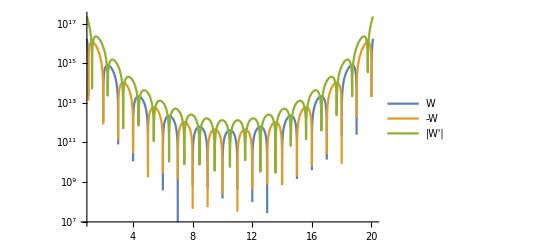

```mathematica
WilkinsonPoly[n_][x_]:=Product[(x-i),{i,1.0,n}]
n=20;
LogPlot[ {WilkinsonPoly[n][x],-WilkinsonPoly[n][x],Abs[WilkinsonPoly[n]'[x]]},{x,0.9,n+0.1},
PlotLegends->{"W","-W","|W'|"}]
```

If I mess with the coefficients just a tiny bit it goes nuts for relatively small n

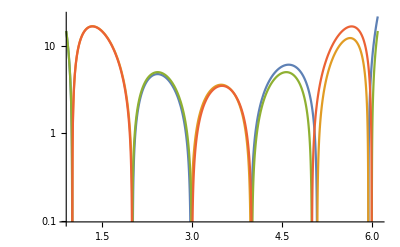

```mathematica
n=6;ϵ=10^-4;
as=CoefficientList[WilkinsonPoly[n][x],x];
bs = as*RandomReal[{1-ϵ,1+ϵ},n+1];
p[cs_][x_]:= Sum[cs[[i]] x^(i-1),{i,Length[cs]}]
LogPlot[ {p[bs][x],-p[bs][x],p[as][x],-p[as][x]},{x,0.9,n+0.1}]
```

The moral of this story is that you can not compute anything that generates the coefficients of even a moderate degree polynomial.

You can not compute eigenvalues by constructing the characteristic polynomial!

In fact, you can (and matlab does) compute polynomial roots by building a matrix!

## Backward Stability and Accuracy

We have an abstract problem f:X→Y with a floating point algorithm f̃:X→Y.

f̃ is accurate if  (|| f̃(x) - f(x) ||)/(||f(x)||)=O(ϵ_mac): 
"Accurate algorithms give nearly the right answer!"

f̃ is backwards stable if  f̃(x) = f(x̃) || for some x̃ satisfying(|| x - x̃ ||)/(||x||)=O(ϵ_machine) 
“Backwards stable algorithm give the right answer to nearly the right question!”

The condition number of f at x∈X is the inherent sensitivity κ(x) of the problem

Theorem 15.1: A backwards stable algorithm f̃ gives relative error O(κ(x)ϵ_machine)
	In symbols,  (|| f̃(x) - f(x) ||)/(||x||)=O(κ(x)ϵ_machine).	
	In practice, the condition number reduces the precision.

This is pretty much exactly what we “think” should happen.

We have a computable "difficulty" for the problem instance "compute f(x)”.  This is the condition number κ(x).

For lots of problems the hidden constant in the “bigO” is O(1). In this case log_10 κ(x) is roughly how many decimal digits you lose.

### Work the Proof